```mathematica
data=Import["/home/freek/Documents/temp2/Introgression/Rfiles/data/loggrowthA.csv"]//Flatten;
```

```mathematica
data=Table[{t,data[[t+1]]},{t,0,19}];
```

```mathematica
nA[nA0_,WA_,t_]:=nA0 WA^t
```

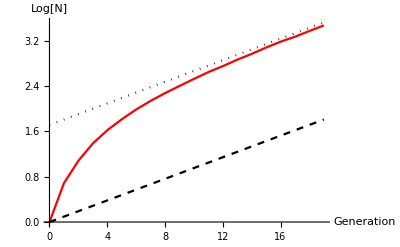

```mathematica
out=Show[
{ListLinePlot[Table[{t,Log[nA[1/0.18,1.1,t]]},{t,0,19}],AxesLabel->{"Generation","Log[N]"},PlotStyle->{Black,Dotted},PlotRange->{Automatic,{0,Automatic}}],ListLinePlot[data,PlotStyle->Red],

ListLinePlot[Table[{t,Log[nA[1,1.1,t]]},{t,0,19}],PlotStyle->{Black,Dashed}]
}
]
```

```mathematica
Export["/home/freek/Documents/temp2/Introgression/Rfiles/figures/PlotSimGrowth.eps",out]
```

/home/freek/Documents/temp2/Introgression/Rfiles/figures/PlotSimGrowth.eps

```mathematica
Clear[nA]
```

```mathematica
RSolve[{p[t+1]==p[t] WA/(p[t]WA+(1-p[t])Wa),p[0]==nA0/(nA0+na0)},p[t],t]//FullSimplify
```

{{p[t]→nA0/(nA0+na0 (Wa/WA)^t)}}